```mathematica
Piecewise[{{0.5u^2, Abs[u]<1}, {Abs[u]-0.5, Abs[u]≥1}}]
```

Piecewise[{{0.5 u^2, Abs[u]<1}, {-0.5+Abs[u], Abs[u]≥1}, {0, True}}]

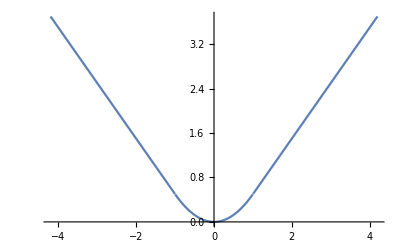

```mathematica
Plot[Piecewise[{{0.5 u^2,Abs[u]<1},{-0.5+Abs[u],Abs[u]≥1}},0],{u,-4.2,4.2}]
```

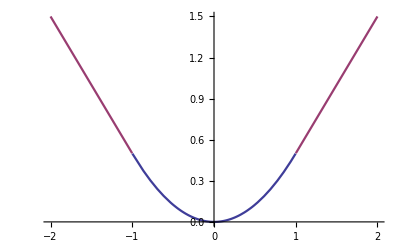

```mathematica
s=Piecewise[{{0.5 #^2,Abs[#]<1},{Abs[#]-0.5,Abs[#]≥1}}]&;

colorFunction=s;
piecewiseParts=Length@colorFunction[[1,1]];
colors=ColorData[1][#]&/@Range@piecewiseParts;
colorFunction[[1,1,All,1]]=colors;

Plot[s[x],{x,-2,2},ColorFunction->colorFunction,ColorFunctionScaling->False]
```

```mathematica
pwSplit[_[pairs:{{_,_}..}]]:=Piecewise[{#},Indeterminate]&/@pairs

pwSplit[_[pairs:{{_,_}..},expr_]]:=Append[pwSplit@{pairs},pwSplit@{{{expr,Nor@@pairs[[All,2]]}}}]
```

```mathematica
pw=Piecewise[{{0.5x^2,Abs[x]<1},{Abs[x]-0.5,Abs[x]≥1}}];
```

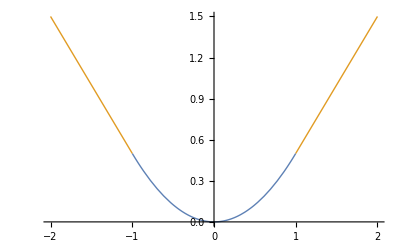

```mathematica
Plot[Evaluate[pwSplit@pw],{x,-2,2},PlotStyle->Thick,Axes->True]
```

```mathematica
Export["smoothl1.png",Plot[Evaluate[pwSplit@pw],{x,-2,2},PlotStyle->Thick,Axes->True],ImageSize->Scaled[.8],ImageResolution->300]
```

smoothl1.png